```mathematica
SetOptions[Plot,BaseStyle->{FontSize->12,Style->{FontColor->Black},AxesStyle->Directive[Black,FontColor->Black]},FrameStyle->Directive[Black,FontColor->Black],AspectRatio->0.75,ImageSize->300];
SetOptions[ListPlot,BaseStyle->{FontSize->12,Style->{FontColor->Black},AxesStyle->Directive[Black,FontColor->Black]},FrameStyle->Directive[Black,FontColor->Black],AspectRatio->1];
SetOptions[ListLinePlot,BaseStyle->{FontSize->12,Style->{FontColor->Black},Frame->True,AxesStyle->Directive[Black,FontColor->Black]},FrameStyle->Directive[Black,FontColor->Black]];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Figure 7

```mathematica
profiles={Import["densityprofile1_experimental_inoculi_Fig7.mat"],Import["densityprofile2_experimental_inoculi_Fig7.mat"],Import["densityprofile3_experimental_inoculi_Fig7.mat"]};
```

General::munfl: 9.44150600030421×10^-309 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.331963757581×10^-311 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.123365857×10^-313 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

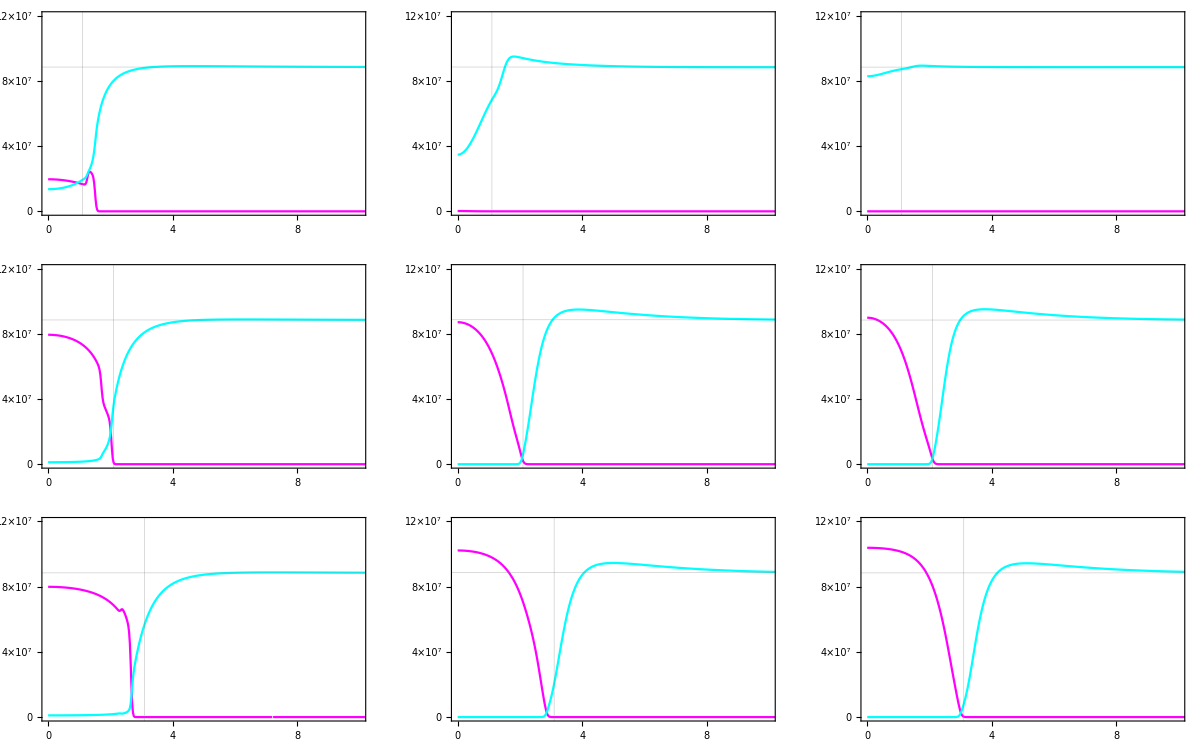

```mathematica
fticks1={{{0,{0.5 10^6,"5×10^5"},{10^6,"1×10^6"}},None},{{0,1,2,3,4,5},None}};
fticks2={{{0,{0.4 10^8,"4×10^7"},{0.8 10^8,"8×10^7"},{12 10^7,"12×10^7"}},None},{{0,2,4,6,8,10},None}};
radiiI=10{0.11,0.21,0.31};
dr=0.025; (* in mm *)
maxK=0.36 0.02 1.2635 10^10;
GraphicsGrid[{With[{i=1},{ListLinePlot[{Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦1⟧]⟦2⟧}],Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦2⟧]⟦2⟧}]},PlotRange->{{0,10},{0,1.2 10^8}},PlotStyle->{Magenta,Cyan},Frame->True,FrameTicks->fticks2,GridLines->{{radiiI⟦i⟧},{Last@Transpose[profiles⟦i⟧⟦2⟧]⟦2⟧}}],ListLinePlot[{Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦1⟧]⟦8⟧}],Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦2⟧]⟦8⟧}]},PlotRange->{{0,10},{0,1.2 10^8}},PlotStyle->{Magenta,Cyan},Frame->True,FrameTicks->fticks2,GridLines->{{radiiI⟦i⟧},{Last@Transpose[profiles⟦i⟧⟦2⟧]⟦3⟧}}],ListLinePlot[{Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦1⟧]⟦14⟧}],Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦2⟧]⟦14⟧}]},PlotRange->{{0,10},{0,1.2 10^8}},PlotStyle->{Magenta,Cyan},Frame->True,FrameTicks->fticks2,GridLines->{{radiiI⟦i⟧},{Last@Transpose[profiles⟦i⟧⟦2⟧]⟦14⟧}}]}],
With[{i=2},{ListLinePlot[{Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦1⟧]⟦2⟧}],Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦2⟧]⟦2⟧}]},PlotRange->{{0,10},{0,1.2 10^8}},PlotStyle->{Magenta,Cyan},Frame->True,FrameTicks->fticks2,GridLines->{{radiiI⟦i⟧},{Last@Transpose[profiles⟦i⟧⟦2⟧]⟦2⟧}}],ListLinePlot[{Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦1⟧]⟦8⟧}],Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦2⟧]⟦8⟧}]},PlotRange->{{0,10},{0,1.2 10^8}},PlotStyle->{Magenta,Cyan},Frame->True,FrameTicks->fticks2,GridLines->{{radiiI⟦i⟧},{Last@Transpose[profiles⟦i⟧⟦2⟧]⟦3⟧}}],ListLinePlot[{Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦1⟧]⟦14⟧}],Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦2⟧]⟦14⟧}]},PlotRange->{{0,10},{0,1.2 10^8}},PlotStyle->{Magenta,Cyan},Frame->True,FrameTicks->fticks2,GridLines->{{radiiI⟦i⟧},{Last@Transpose[profiles⟦i⟧⟦2⟧]⟦14⟧}}]}],
With[{i=3},{ListLinePlot[{Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦1⟧]⟦2⟧}],Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦2⟧]⟦2⟧}]},PlotRange->{{0,10},{0,1.2 10^8}},PlotStyle->{Magenta,Cyan},Frame->True,FrameTicks->fticks2,GridLines->{{radiiI⟦i⟧},{Last@Transpose[profiles⟦i⟧⟦2⟧]⟦2⟧}}],ListLinePlot[{Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦1⟧]⟦8⟧}],Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦2⟧]⟦8⟧}]},PlotRange->{{0,10},{0,1.2 10^8}},PlotStyle->{Magenta,Cyan},Frame->True,FrameTicks->fticks2,GridLines->{{radiiI⟦i⟧},{Last@Transpose[profiles⟦i⟧⟦2⟧]⟦3⟧}}],ListLinePlot[{Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦1⟧]⟦14⟧}],Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦2⟧]⟦14⟧}]},PlotRange->{{0,10},{0,1.2 10^8}},PlotStyle->{Magenta,Cyan},Frame->True,FrameTicks->fticks2,GridLines->{{radiiI⟦i⟧},{Last@Transpose[profiles⟦i⟧⟦2⟧]⟦14⟧}}]}]}]
```

```mathematica
areas=Flatten[Import["area_K1_experimental_inoculi_Fig7.mat"],1];
areas=Table[Drop[areas⟦i⟧,1],{i,Length[areas]}];
pops=Flatten[Import["cellabundance_K1_experimental_inoculi_Fig7.mat"],1];
pops=Table[Drop[pops⟦i⟧,1],{i,Length[pops]}];
```

{0.10102,0.0150503,0.752792,0.0648503,0.0207636,0.769192,0.604518,0.994698,0.,0.938422,0.988709,0.0359433,0.762119,0.0394188,0.211526,0.471705,1.,0.305195,0.570859,0.412448,0.973652,0.886553}

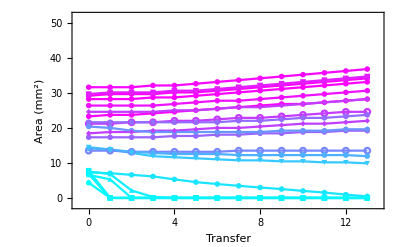

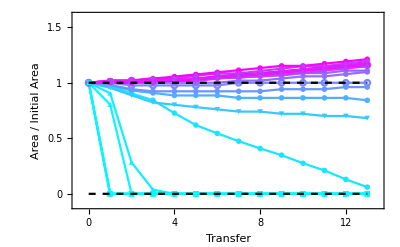

```mathematica
colorBlends=(pops⟦All,1⟧-Min[pops⟦All,1⟧])/(Max[pops⟦All,1⟧]-Min[pops⟦All,1⟧])
colors=Blend[{Cyan,Magenta},#]&/@colorBlends;
pA=ListLinePlot[Table[Transpose[{Table[j-1,{j,Length[areas⟦i⟧]}],areas⟦i⟧}],{i,Length[areas]}],PlotMarkers->{Automatic,0.03},PlotStyle->colors,Frame->True,FrameLabel->{"Transfer","Area (mm^2)"},PlotRange->{{-0.5,13.5},{-2,52}},FrameTicks->{{{0,10,20,30,40,50},None},{{0,4,8,12},None}}]
pRatio=Show[ListLinePlot[Table[Transpose[{Table[j-1,{j,Length[areas⟦i⟧]}],areas⟦i⟧/areas⟦i⟧⟦1⟧}],{i,Length[areas]}],PlotMarkers->{Automatic,0.03},PlotStyle->colors,Frame->True,FrameLabel->{"Transfer","Area / Initial Area"},PlotRange->{{-0.5,13.5},{-0.1,1.6}},FrameTicks->{{{0,0.5,1,1.5},None},{{0,4,8,12},None}}],Plot[{0,1},{x,0,13},PlotStyle->{{Dashed,Black}}]]
```

## Figure 7 supplement 1

```mathematica
profiles={Import["densityprofile1_idealized_inoculi_Fig7.mat"],Import["densityprofile2_idealized_inoculi_Fig7.mat"],Import["densityprofile3_idealized_inoculi_Fig7.mat"]};
```

General::munfl: 2.278216703006×10^-310 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.4911102258×10^-312 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.5511940614792×10^-309 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

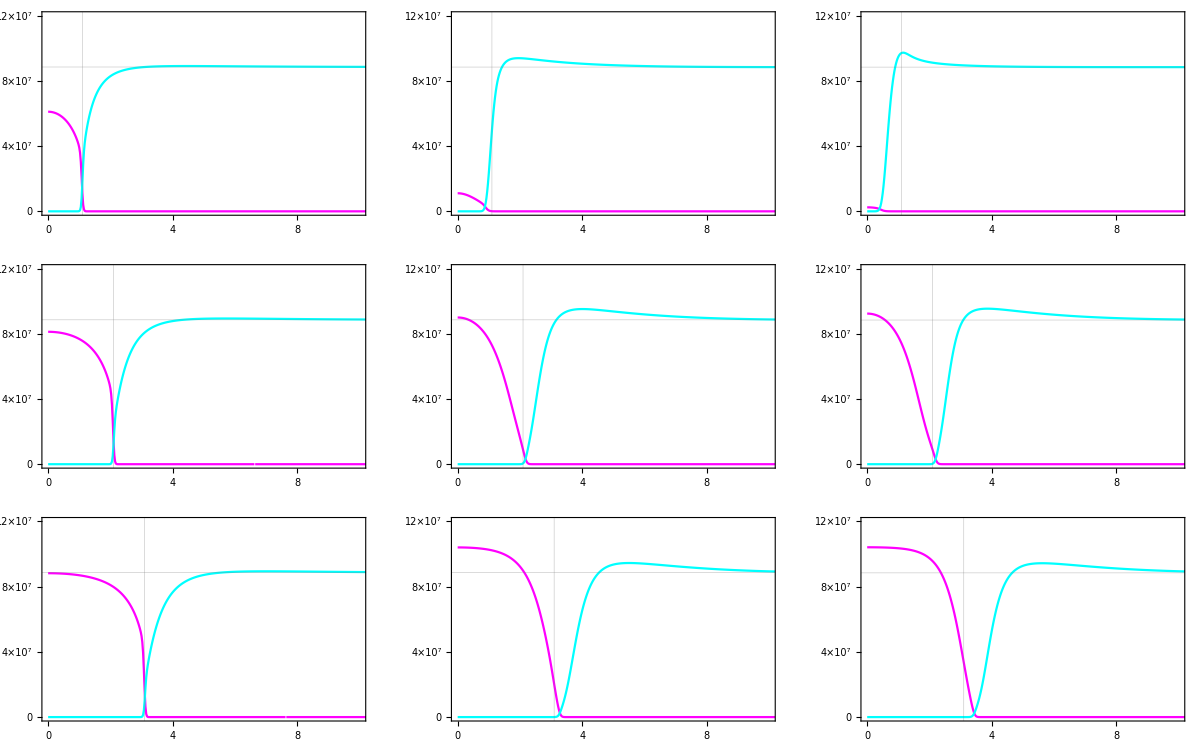

```mathematica
fticks1={{{0,{0.5 10^6,"5×10^5"},{10^6,"1×10^6"}},None},{{0,1,2,3,4,5},None}};
fticks2={{{0,{0.4 10^8,"4×10^7"},{0.8 10^8,"8×10^7"},{12 10^7,"12×10^7"}},None},{{0,2,4,6,8,10},None}};
radiiI=10{0.11,0.21,0.31};
dr=0.025; (* in mm *)
maxK=0.36 0.02 1.2635 10^10;
GraphicsGrid[{With[{i=1},{ListLinePlot[{Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦1⟧]⟦2⟧}],Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦2⟧]⟦2⟧}]},PlotRange->{{0,10},{0,1.2 10^8}},PlotStyle->{Magenta,Cyan},Frame->True,FrameTicks->fticks2,GridLines->{{radiiI⟦i⟧},{Last@Transpose[profiles⟦i⟧⟦2⟧]⟦2⟧}}],ListLinePlot[{Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦1⟧]⟦8⟧}],Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦2⟧]⟦8⟧}]},PlotRange->{{0,10},{0,1.2 10^8}},PlotStyle->{Magenta,Cyan},Frame->True,FrameTicks->fticks2,GridLines->{{radiiI⟦i⟧},{Last@Transpose[profiles⟦i⟧⟦2⟧]⟦3⟧}}],ListLinePlot[{Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦1⟧]⟦14⟧}],Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦2⟧]⟦14⟧}]},PlotRange->{{0,10},{0,1.2 10^8}},PlotStyle->{Magenta,Cyan},Frame->True,FrameTicks->fticks2,GridLines->{{radiiI⟦i⟧},{Last@Transpose[profiles⟦i⟧⟦2⟧]⟦14⟧}}]}],
With[{i=2},{ListLinePlot[{Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦1⟧]⟦2⟧}],Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦2⟧]⟦2⟧}]},PlotRange->{{0,10},{0,1.2 10^8}},PlotStyle->{Magenta,Cyan},Frame->True,FrameTicks->fticks2,GridLines->{{radiiI⟦i⟧},{Last@Transpose[profiles⟦i⟧⟦2⟧]⟦2⟧}}],ListLinePlot[{Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦1⟧]⟦8⟧}],Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦2⟧]⟦8⟧}]},PlotRange->{{0,10},{0,1.2 10^8}},PlotStyle->{Magenta,Cyan},Frame->True,FrameTicks->fticks2,GridLines->{{radiiI⟦i⟧},{Last@Transpose[profiles⟦i⟧⟦2⟧]⟦3⟧}}],ListLinePlot[{Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦1⟧]⟦14⟧}],Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦2⟧]⟦14⟧}]},PlotRange->{{0,10},{0,1.2 10^8}},PlotStyle->{Magenta,Cyan},Frame->True,FrameTicks->fticks2,GridLines->{{radiiI⟦i⟧},{Last@Transpose[profiles⟦i⟧⟦2⟧]⟦14⟧}}]}],
With[{i=3},{ListLinePlot[{Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦1⟧]⟦2⟧}],Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦2⟧]⟦2⟧}]},PlotRange->{{0,10},{0,1.2 10^8}},PlotStyle->{Magenta,Cyan},Frame->True,FrameTicks->fticks2,GridLines->{{radiiI⟦i⟧},{Last@Transpose[profiles⟦i⟧⟦2⟧]⟦2⟧}}],ListLinePlot[{Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦1⟧]⟦8⟧}],Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦2⟧]⟦8⟧}]},PlotRange->{{0,10},{0,1.2 10^8}},PlotStyle->{Magenta,Cyan},Frame->True,FrameTicks->fticks2,GridLines->{{radiiI⟦i⟧},{Last@Transpose[profiles⟦i⟧⟦2⟧]⟦3⟧}}],ListLinePlot[{Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦1⟧]⟦14⟧}],Transpose[{Table[dr (j-1),{j,Length[profiles⟦i⟧⟦1⟧]}],Transpose[profiles⟦i⟧⟦2⟧]⟦14⟧}]},PlotRange->{{0,10},{0,1.2 10^8}},PlotStyle->{Magenta,Cyan},Frame->True,FrameTicks->fticks2,GridLines->{{radiiI⟦i⟧},{Last@Transpose[profiles⟦i⟧⟦2⟧]⟦14⟧}}]}]}]
```

```mathematica
areas=Flatten[Import["area_K1_idealized_inoculi_Fig7.mat"],1];
areas=Table[Drop[areas⟦i⟧,1],{i,Length[areas]}];
pops=Flatten[Import["cellabundance_K1_idealized_inoculi_Fig7.mat"],1];
pops=Table[Drop[pops⟦i⟧,1],{i,Length[pops]}];
```

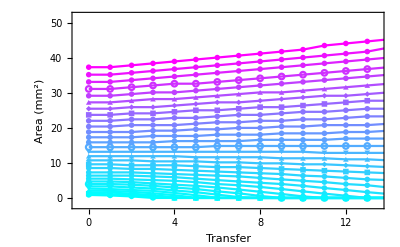

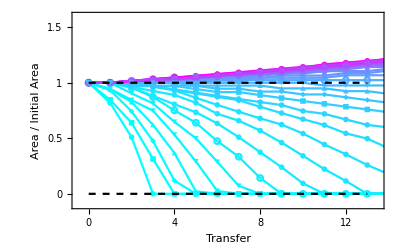

```mathematica
colorBlends=(pops⟦All,1⟧-Min[pops⟦All,1⟧])/(Max[pops⟦All,1⟧]-Min[pops⟦All,1⟧]);
colors=Blend[{Cyan,Magenta},#]&/@colorBlends;
pA=ListLinePlot[Table[Transpose[{Table[j-1,{j,Length[areas⟦i⟧]}],areas⟦i⟧}],{i,Length[areas]}],PlotMarkers->{Automatic,0.03},PlotStyle->colors,Frame->True,FrameLabel->{"Transfer","Area (mm^2)"},PlotRange->{{-0.5,13.5},{-2,52}},FrameTicks->{{{0,10,20,30,40,50},None},{{0,4,8,12},None}}]
pRatio=Show[ListLinePlot[Table[Transpose[{Table[j-1,{j,Length[areas⟦i⟧]}],areas⟦i⟧/areas⟦i⟧⟦1⟧}],{i,Length[areas]}],PlotMarkers->{Automatic,0.03},PlotStyle->colors,Frame->True,FrameLabel->{"Transfer","Area / Initial Area"},PlotRange->{{-0.5,13.5},{-0.1,1.6}},FrameTicks->{{{0,0.5,1,1.5},None},{{0,4,8,12},None}}],Plot[{0,1},{x,0,13},PlotStyle->{{Dashed,Black}}]]
```